```mathematica
ClearAll["Global`*"]
```

```mathematica
importdirectory=NotebookDirectory[]<>"../Data"
SetDirectory[importdirectory];
legendstyle={FontSize->08,Bold};
labelstyle={FontFamily->"Helvetica", 18, GrayLevel[0]};
basestyle={FontFamily->"Helvetica", FontSize->18};
PrefColors={RGBColor[0.857359, 0.131106, 0.132128],RGBColor[0.8935136, 0.6004149999999999, 0.2205464],RGBColor[0.6660832000000001, 0.7430418, 0.3229354],RGBColor[0.38822480000000004, 0.674195, 0.6035436000000001],RGBColor[0.2484884, 0.3863264, 0.813373],RGBColor[0.471412, 0.108766, 0.527016],GrayLevel[0]};
PrefColors2={-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-};
```

/Users/Michael/Dropbox/Research/ECFL/2D/2D-ECFL-Template-2022/ShareWithSam/2Du0sumrule2ndOrderDFTIchi2022template/Plots/../Data

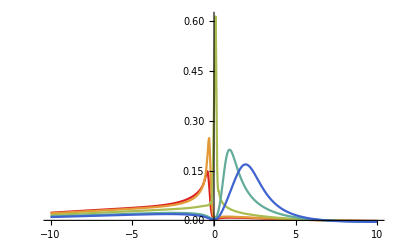

```mathematica
data=Import["Spectrum/bigG_nodal_cmplx{Nomega2E10, Nk016, nd0.850, tau0.057,"<>
" tp-0.200, tpp0.000, J0.170, mup-1.000, u0_2.500, dom50}SUCCESS.dat"];
reG=Interpolation[Map[{{#[[1]],#[[2]]},#[[3]]}&,data]];
imG=Interpolation[Map[{{#[[1]],#[[2]]},#[[4]]}&,data]];
G[q_,ω_]:=reG[q,ω]+I*imG[q,ω];
qset={0,π/4,π/2,3π/4,π};
plotdata=Table[-1/π*Im[G[q,ω]],{q,qset}];
Plot[Evaluate[plotdata],
	{ω,-10,10},
	PlotStyle->PrefColors,
	PlotRange->All]
```

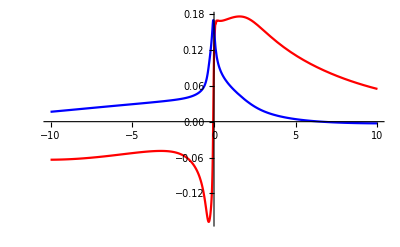

```mathematica
data=Import["Spectrum/bigG_loc_cmplx{Nomega2E12, Nk032, nd0.850, tau0.057, tp-0.200,"<>
" tpp0.000, J0.170, mup-1.000, u0_2.500, neta07, dom50}SUCCESS.dat"];
reGloc=Interpolation[Map[{#[[1]],#[[2]]}&,data]];
imGloc=Interpolation[Map[{#[[1]],#[[3]]}&,data]];
Gloc[ω_]:=reGloc[ω]+I*imGloc[ω];
Plot[{Re[Gloc[ω]],-1/π*Im[Gloc[ω]]},
	{ω,-10,10},
	PlotStyle->{Red,Blue},
	PlotRange->All]
```

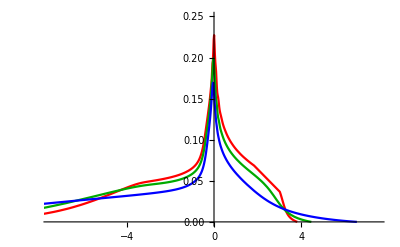

```mathematica
data=Import["Spectrum/bigG_loc_cmplx{Nomega2E12, Nk032, nd0.750, tau0.057, tp-0.200,"<>
" tpp0.000, J0.170, mup-1.000, u0_2.500, neta07, dom50}SUCCESS.dat"];
reGloc1=Interpolation[Map[{#[[1]],#[[2]]}&,data]];
imGloc1=Interpolation[Map[{#[[1]],#[[3]]}&,data]];
Gloc1[ω_]:=reGloc1[ω]+I*imGloc1[ω];
data=Import["Spectrum/bigG_loc_cmplx{Nomega2E12, Nk032, nd0.800, tau0.057, tp-0.200,"<>
" tpp0.000, J0.170, mup-1.000, u0_2.500, neta07, dom50}SUCCESS.dat"];
reGloc2=Interpolation[Map[{#[[1]],#[[2]]}&,data]];
imGloc2=Interpolation[Map[{#[[1]],#[[3]]}&,data]];
Gloc2[ω_]:=reGloc2[ω]+I*imGloc2[ω];
data=Import["Spectrum/bigG_loc_cmplx{Nomega2E12, Nk032, nd0.850, tau0.057, tp-0.200,"<>
" tpp0.000, J0.170, mup-1.000, u0_2.500, neta07, dom50}SUCCESS.dat"];
reGloc3=Interpolation[Map[{#[[1]],#[[2]]}&,data]];
imGloc3=Interpolation[Map[{#[[1]],#[[3]]}&,data]];
Gloc3[ω_]:=reGloc3[ω]+I*imGloc3[ω];

plotdata={-1/π*Im[Gloc1[ω]],-1/π*Im[Gloc2[ω]],-1/π*Im[Gloc3[ω]]};
Plot[Evaluate[plotdata],
	{ω,-30,30},
	PlotStyle->{Red, Darker[Green],Blue},
	PlotRange->{{-7.5,7.5},{0,0.25}}
]
```

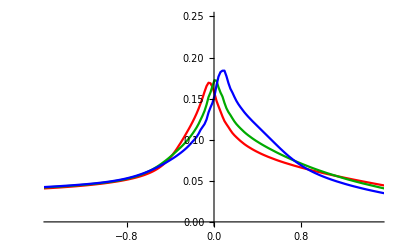

```mathematica
data=Import["Spectrum/bigG_loc_cmplx{Nomega2E12, Nk032, nd0.850, tau0.057, tp-0.200,"<>
" tpp0.000, J0.170, mup-1.000, u0_2.500, neta07, dom50}SUCCESS.dat"];
reGloc1=Interpolation[Map[{#[[1]],#[[2]]}&,data]];
imGloc1=Interpolation[Map[{#[[1]],#[[3]]}&,data]];
Gloc1[ω_]:=reGloc1[ω]+I*imGloc1[ω];
data=Import["Spectrum/bigG_loc_cmplx{Nomega2E12, Nk032, nd0.850, tau0.057, tp0.000,"<>
" tpp0.000, J0.170, mup-1.000, u0_2.500, neta07, dom50}SUCCESS.dat"];
reGloc2=Interpolation[Map[{#[[1]],#[[2]]}&,data]];
imGloc2=Interpolation[Map[{#[[1]],#[[3]]}&,data]];
Gloc2[ω_]:=reGloc2[ω]+I*imGloc2[ω];
data=Import["Spectrum/bigG_loc_cmplx{Nomega2E12, Nk032, nd0.850, tau0.057, tp0.200,"<>
" tpp0.000, J0.170, mup-1.000, u0_2.500, neta07, dom50}SUCCESS.dat"];
reGloc3=Interpolation[Map[{#[[1]],#[[2]]}&,data]];
imGloc3=Interpolation[Map[{#[[1]],#[[3]]}&,data]];
Gloc3[ω_]:=reGloc3[ω]+I*imGloc3[ω];

plotdata={-1/π*Im[Gloc1[ω]],-1/π*Im[Gloc2[ω]],-1/π*Im[Gloc3[ω]]};
Plot[Evaluate[plotdata],
	{ω,-30,30},
	PlotStyle->{Red, Darker[Green],Blue},
	PlotRange->{{-1.5,1.5},{0,0.25}}
]
```